# Final Project: Constructing Regular Polygons from Euclid’s Elements

### By: Ethan Remsberg

## Constructing Angles

All of Euclid’s proofs assume that the only tools you have are a compass and a straightedge. Without a protractor, drawing precise angles is not possible (and would make these problems trivial). Instead, angles are often constructed by copying an already existing angle. This is possible using just a compass and straightedge.

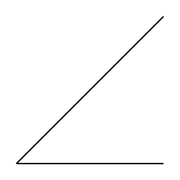

```mathematica
b = {0, 0};
c = {4, 0};
a = {4, 4};
Graphics[{Line[{a,b}], Line[{c, b}]}, ImageSize->Small]
```

Let this angle ABC be the one we want to copy. We begin by drawing an arc centered at the vertex B.

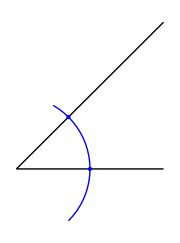

```mathematica
x = {Sqrt[2], Sqrt[2]};
y = {2, 0};
angle1 =Graphics[{Line[{a,b}], Line[{c, b}], Blue, Circle[{0, 0}, 2, {-π/4, π/3}], Point[{x, y}]}, ImageSize->Small]
```

The points of intersection of the arc and the rays AB and BC will be denoted X and Y, respectively. Using a compass, we can draw an arc of the same radius onto any new straight line.

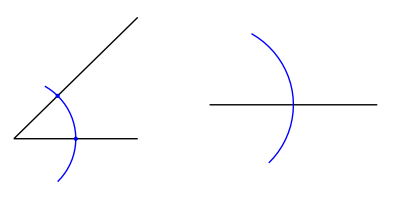

```mathematica
angle2 = Graphics[{Line[{c, b}], Blue, Circle[{0, 0}, 2, {-π/4, π/3}]}, ImageSize->Small];
GraphicsGrid[{{angle1, angle2}}]
```

Then, using the compass, we are able to copy the straight-line distance between X and Y. This can be transferred onto our new angle to find the third vertex of the angle.

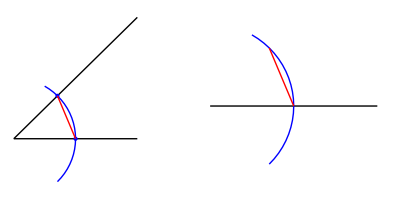

```mathematica
angle1 =Graphics[{Line[{a,b}], Line[{c, b}], Blue, Circle[{0, 0}, 2, {-π/4, π/3}], Point[{x, y}], Red, Line[{x, y}]}, ImageSize->Small];
angle2 = Graphics[{Line[{c, b}], Blue, Circle[{0, 0}, 2, {-π/4, π/3}], Red, Line[{x, y}]}, ImageSize->Small];
GraphicsGrid[{{angle1, angle2}}]
```

Using the straightedge allows us to complete the angle.

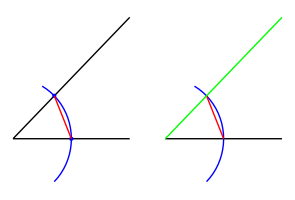

```mathematica
angle2 = Graphics[{Line[{c, b}], Blue, Circle[{0, 0}, 2, {-π/4, π/3}], Red, Line[{x, y}], Green, Line[{b, a}]}, ImageSize->Small];
GraphicsGrid[{{angle1, angle2}}]
```

On the right, the angle formed by the black and green lines is equivalent to the angle on the left.

## Constructing an Equilateral Triangle

Euclid begins his proofs in Book IV with the inscription of any triangle inside a circle. In particular, this proposition can be used to inscribe an equilateral triangle inside a circle. To do this, we only need a 60° angle, along with our straightedge and compass. The process is as follows:
	1) Draw a circle, and a line that touches the circle at exactly one point. These are the black lines.
	2) Copy the 60° angle such that the vertex is at the intersection point of the line and circle. Do this from each endpoint on the line. These are the blue lines.
	3) Extend the blue lines until they intersect the circle. Connect these new intersections of the circle and the blue lines. This is the red line.
	
This is now an equiangular triangle inscribed in a circle, exactly as we wanted. In general, if you wanted to inscribe a non-regular triangle, you would need a copy of the triangle you’re trying to inscribe. Then, instead of copying the same angle twice, you instead would copy two different angles from the triangle.

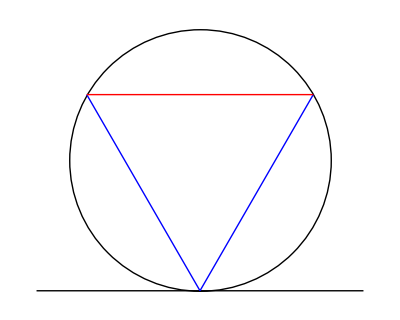

```mathematica
g = {-5, -4};
h = {5, -4};
a = {0, -4};
c = a.RotationMatrix[2π/3];
b = a.RotationMatrix[-2π/3];
Graphics[{Circle[{0, 0}, 4],Line[{g, h}], Blue, Line[{a, c}], Line[{a, b}], Red, Line[{b, c}]}, PlotRange->5]
```

## Bisecting Line Segments

It is worth noting that the term “straightedge” does not imply that is marked; that is, the straightedge is NOT a ruler and cannot measure distances (again, having this ability would somewhat trivialize the problem). In the subsequent proofs, we need the ability to bisect line segments. While the task of finding the midpoint of a line would be made easier with a marked straightedge, it is possible, and quite simple, to do with just a compass and non-marked straightedge.

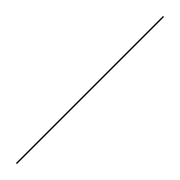

```mathematica
a = {-2, -2};
b = {2, 2};
Graphics[Line[{a, b}], PlotRange->3, ImageSize->Small]
```

Say we want to draw a line that bisects this line segment. We begin by drawing arcs from both endpoints.

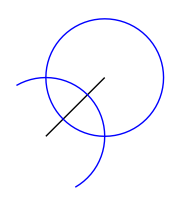

```mathematica
Graphics[{Line[{a, b}], Blue,Circle[a, 4, {-π/3, 2π/3}], Circle[b, 4, {-π/2, 3π/2}]}, PlotRange->4, ImageSize->Small]
```

Then, if we connect the intersections of these two arcs, we will have created a perpendicular bisector of the original line.

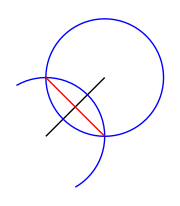

```mathematica
Graphics[{Line[{a, b}], Blue,Circle[a, 4, {-π/3, 2π/3}], Circle[b, 4, {-π/2, 3π/2}], Red, Line[{{2, -2}, {-2, 2}}]}, PlotRange->4, ImageSize->Small]
```

The red line is the requested bisection of the original line.

## Constructing a Regular Pentagon

Now that we are able to inscribe triangles in a circle and bisect lines, we can construct a regular pentagon. We begin by inscribing an isosceles triangle into a circle. As noted above, this is possible if we are given a copy of the triangle to begin with.

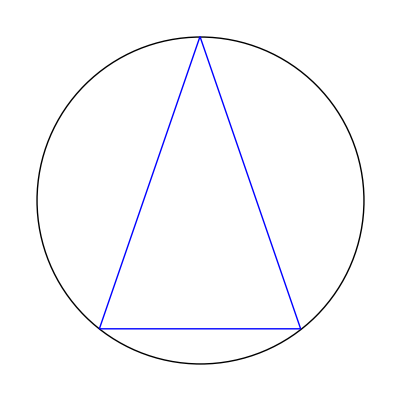

```mathematica
a = {0, 4};
d = -a.RotationMatrix[-38*Degree];
c = -a.RotationMatrix[38 *Degree];
Graphics[{Black, Circle[{0, 0}, 4],Blue, Line[{a, c}], Line[{a, d}], Line[{c, d}]}]
```

Now,  we can bisect the two equal sides of the isosceles triangle, thus finding the midpoint. Then, we connect the midpoint to the vertex opposite of the side of the triangle and extend it to intersect the circle.

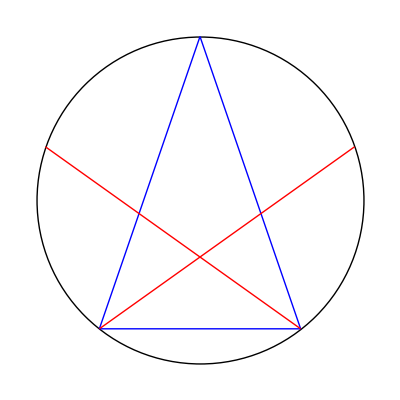

```mathematica
e = (a + d);
e = 4 * (e / Norm[e]);
b = (a + c);
b = 4 * (b / Norm[b]);
Graphics[{Black, Circle[{0, 0}, 4],Blue, Line[{a, c}], Line[{a, d}], Line[{c, d}], Red, Line[{c, e}], Line[{b, d}]}]
```

Finally, connecting all of the points on the circle yields a regular pentagon.

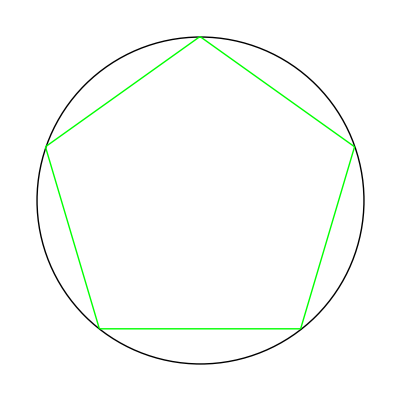

```mathematica
Graphics[{Black, Circle[{0, 0}, 4], Green, Line[{a, b}], Line[{b, c}], Line[{d, e}], Line[{e, a}], Line[{c, d}]}]
```

Up until now, we have not taken into consideration the orientation of the shapes we draw or the size of the circle. Perhaps unsurprisingly, these things do not matter, but here’s proof if you’re not convinced. You can stretch and rotate the plot as much as you want and the pentagon will still be regular. Perhaps the most revealing insight is if you move the locator to each vertex of the pentagon. While the triangle itself changes, the pentagon does not.

```mathematica
Manipulate[Graphics[{Black, Circle[{0, 0}, Norm[p]], Green, Line[{p, (Norm[p] / Norm[p + RotationMatrix[π/5].(-p)])*(p + RotationMatrix[π/5].(-p))}], Line[{(Norm[p] / Norm[p + RotationMatrix[π/5].(-p)])*(p + RotationMatrix[π/5].(-p)), RotationMatrix[π/5].(-p)}], Line[{RotationMatrix[-π/5].(-p), (Norm[p] / Norm[p + RotationMatrix[-π/5].(-p)])*(p + RotationMatrix[-π/5].(-p))}], Line[{(Norm[p] / Norm[p + RotationMatrix[-π/5].(-p)])*(p + RotationMatrix[-π/5].(-p)), p}], Line[{RotationMatrix[π/5].(-p), RotationMatrix[-π/5].(-p)}],Blue, Line[{p, RotationMatrix[π/5].(-p)}], Line[{RotationMatrix[π/5].(-p), RotationMatrix[-π/5].(-p)}], Line[{p, RotationMatrix[-π/5].(-p)}]}, PlotRange-> 5], {{p, {0, 4}}, Locator}]
```

```mathematica
d =RotationMatrix[-π/5].(-p);
c =RotationMatrix[π/5].(-p);
e = (Norm[p] / Norm[p + RotationMatrix[-π/5].(-p)])*(p+ RotationMatrix[-π/5].(-p));
b = (Norm[p] / Norm[p + RotationMatrix[π/5].(-p)])*(p+ RotationMatrix[π/5].(-p));
```

## Constructing a Regular Hexagon

This proof is a bit different from the rest. We begin by drawing a diameter on the circle. Then, we draw a new circle centered at one endpoint of this diameter and that has a radius the same as the original circle.

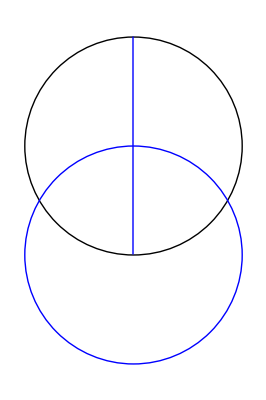

```mathematica
a = {0,4};
Graphics[{Circle[{0, 0}, Norm[a]], Blue, Line[{a, -a}], Circle[-a, Norm[a]]}]
```

From here, we draw lines from the intersections of the two circles through the center of the original, and we extend these lines so that they intersect the original circle.

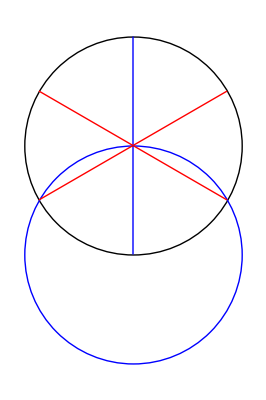

```mathematica
Graphics[{Circle[{0, 0}, Norm[a]], Blue, Line[{a, -a}], Circle[-a, Norm[a]],Red, Line[{a . RotationMatrix[-2π/ 3], {0, 0}}], Line[{-a . RotationMatrix[-2π/ 3], {0, 0}}], Line[{-a . RotationMatrix[2π/ 3], {0, 0}}], Line[{a . RotationMatrix[2π/ 3],{0, 0}}]}]
```

Connecting all 6 points that lie on the original circle yield a regular hexagon.

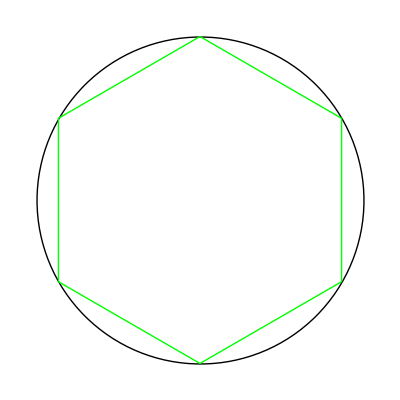

```mathematica
Graphics[{Circle[{0, 0}, 4],Green, Line[{a, -a . RotationMatrix[-2π/ 3]}], Line[{-a . RotationMatrix[-2π/ 3], a . RotationMatrix[2π/ 3]}], Line[{a . RotationMatrix[2π/ 3], -a}], Line[{-a, a . RotationMatrix[-2π/ 3]}], Line[{a . RotationMatrix[-2π/ 3], -a . RotationMatrix[2π/ 3]}], Line[{-a . RotationMatrix[2π/ 3], a}]}]
```

Once again, we can show that the orientation of the circle and the size of the circle do not affect the hexagon. As before, while the intermediates may change as you move the Locator, the hexagon itself will remain regular.

```mathematica
Manipulate[Graphics[{Circle[{0, 0}, Norm[a]], Blue, Line[{a, -a}], Circle[-a, Norm[a]], Red, Line[{a . RotationMatrix[-2π/ 3], {0, 0}}], Line[{-a . RotationMatrix[-2π/ 3], {0, 0}}], Line[{a . RotationMatrix[2π/ 3],{0, 0}}], Line[{-a . RotationMatrix[2π/ 3], {0, 0}}], Green, Line[{a, -a . RotationMatrix[-2π/ 3]}], Line[{-a . RotationMatrix[-2π/ 3], a . RotationMatrix[2π/ 3]}], Line[{a . RotationMatrix[2π/ 3], -a}], Line[{-a, a . RotationMatrix[-2π/ 3]}], Line[{a . RotationMatrix[-2π/ 3], -a . RotationMatrix[2π/ 3]}], Line[{-a . RotationMatrix[2π/ 3], a}]}, PlotRange->10], {{a, {0, 4}}, Locator}]
```

## Constructing a Regular 15-gon

Now we can get to the most interesting result of Euclid’s works. Euclid proves that a regular 15-gon can be inscribed in a circle, using the facts about inscribing an equilateral triangle and a regular pentagon (proven above).  We begin by drawing one side of the triangle and one side of the pentagon in our circle. These are the blue lines. Then, we can find the midpoint of the line defined by the intersection of the circle with these blue lines by bisecting it.  Extending this bisection to the circle and connecting the two blue lines to it yields two sides of our 15-gon.

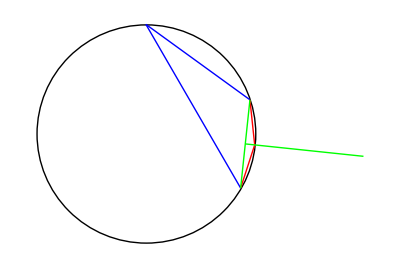

```mathematica
a = {0,1};
c = a.RotationMatrix[2π/3];
b = a.RotationMatrix[2π/5];
e = a.RotationMatrix[(2π/3 - 2π/5) / 2 + 2π/5];

c2 = c.RotationMatrix[(2π/3 - 2π/5) / 2];
b2 = b.RotationMatrix[(2π/3 - 2π/5) / 2];
e2 = e.RotationMatrix[(2π/3 - 2π/5) / 2];

Graphics[{Circle[{0, 0}, 1],Blue, Line[{a, b}], Line[{a, c}],Red, Line[{b, e}], Line[{c, e}], Green, Line[{b, c}], Line[{(b + c) / 2, 2* e}]}, PlotRange->1.25]
```

Now, we have one angle of the regular 15-gon. At this point, we can copy this angle all the way around the circle to get our perfect 15-gon. As proof, I rotated the sides of the triangle and pentagon (the blue lines), by this same angle to ensure that they match up. The dashed blue lines are the lines from the previous step, and the solid blue lines are the result of rotating by the angle of the 15-gon. As you can see things line up perfectly with the regular 15-gon.

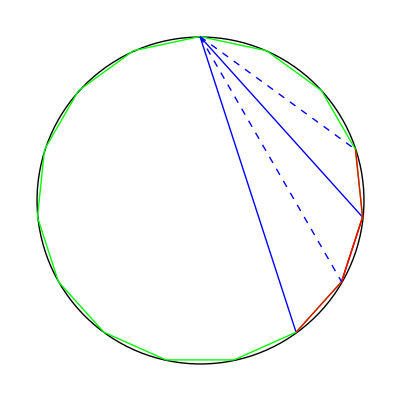

```mathematica
Graphics[{Circle[{0, 0}, 1],Blue,Line[{a, c2}], Line[{a, b2}], Green, Line[{CirclePoints[15]}], Line[{CirclePoints[15][[1]], CirclePoints[15][[15]]}], Red, Line[{b, e}], Line[{c, e}], Line[{b2, e2}], Line[{c2, e2}], Dashed, Blue,Line[{a, b}], Line[{a, c}]}, PlotRange->1.25]
```

### A Note on Regular mn-gons

While this result is certainly interesting, it has an even more resounding extension. This method, in general can be used to inscribe any mn-gon inside a circle if the following hold:
	1) Both an m-gon and an n-gon are constructible.
	2) m and n are relatively prime.
In the case above, we are inscribing a 5*3-gon, and we know that we can inscribe a regular pentagon and triangle. Also, 3 and 5 are relatively prime. This is seen in the proof, too; we needed one side of each of these polygons for it to work. But, for example, if you tried to inscribe an 18-gon using a triangle and a hexagon, it wouldn’t work, because 3 and 6 are not relatively prime. Why?

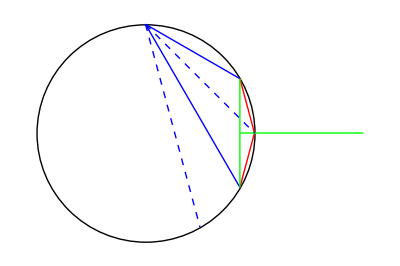

```mathematica
a = {0, 1};
b1 = a.RotationMatrix[2π/3];
c1 = a.RotationMatrix[π/3];
e1 = a.RotationMatrix[π/6 + π/3];

b2 = b1.RotationMatrix[π/6];
c2 = c1.RotationMatrix[π/6];
Graphics[{Circle[{0, 0}, 1], Blue,Line[{a, b1}], Line[{a, c1}], Red, Line[{c1, e1}], Line[{b1, e1}], Green, Line[{b1, c1}], Line[{(b1 + c1) / 2, 2 * e1}], Blue,Dashed,Line[{a, c2}], Line[{a, b2}]}, PlotRange->1.25]
```

After the first two iterations, things seem to work fine. However, if we iterate this process, say, 12 more times...

```mathematica
b9 = b1;
c9 = c1;
For[i = 0, i < 12, i++, b9 = b9.RotationMatrix[π/6]]
For[i = 0, i < 12, i++, c9 = c9.RotationMatrix[π/6]]
```

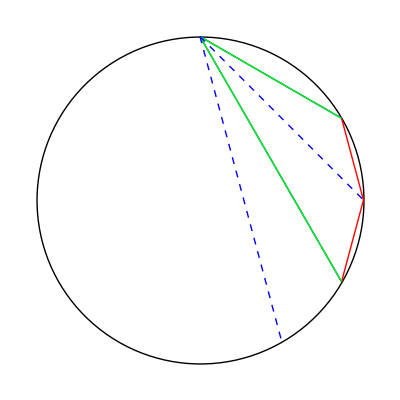

```mathematica
Graphics[{Circle[{0, 0}, 1], Blue,Line[{a, b1}], Line[{a, c1}], Red, Line[{c1, e1}], Line[{b1, e1}],Green,Line[{a, c9}], Line[{a, b9}], Blue,Dashed,Line[{a, c2}], Line[{a, b2}]}, PlotRange->1.25]
```

...then the lines begin to overlap themselves. The dotted green lines are 12 iterations after the solid blue lines, yet they overlap anyway. We would expect this after all 18 iterations have been executed all 18 sides have been drawn. As a result, we would begin drawing lines over already existing lines and thus never get to 18 sides. If the m and n are co-prime, this overlap will not happen until all of the sides have been drawn.

## Constructing a 2^n-gon

One more interesting result arises with the idea of bisecting lines. If we have an even number of lines in a regular polygon, then we can bisect all of those lines and still have a regular polygon. Thus, we can form any 2^n-gon just by bisecting lines. Of course, n must be greater than 1, since there is no 2-gon. So, we can begin with a regular 4-gon, that is, a square. We draw one diameter, and then draw another by bisecting the first one. Connecting the points on the circle gives us our square.

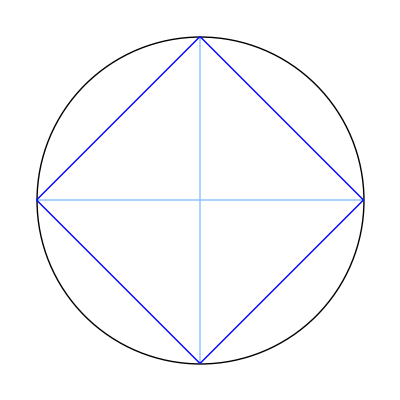

```mathematica
a = {0, 4};
b = -a;
c = {4, 0};
d = -c;

e = {2 * Sqrt[2], 2 * Sqrt[2]};
f = -e;
g= {-2 * Sqrt[2], 2 * Sqrt[2]};
h = -g;
Graphics[{Circle[{0, 0}, 4], RGBColor[0.53,0.74,1.], Line[{a, b}], Line[{c, d}], Blue,Line[{a, c}], Line[{a, d}], Line[{b, c}], Line[{b, d}]}]
```

Then from here, we can apply the same process and bisect all four sides of the square. Then, connecting all of the points on the circle gives us our regular octagon.

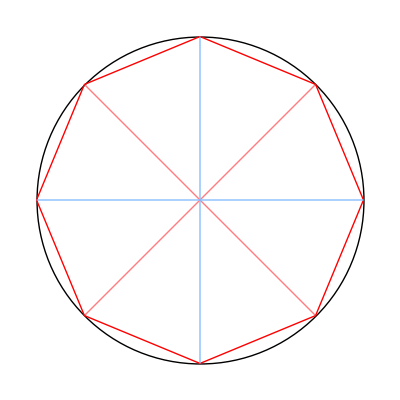

```mathematica
Graphics[{Circle[{0, 0}, 4], RGBColor[1.,0.49,0.5], Line[{e,f}], Line[{g, h}], Red, Line[{a, e}], Line[{e, c}], Line[{c, h}], Line[{h, b}], Line[{b, f}], Line[{f, d}], Line[{d, g}], Line[{g, a}], RGBColor[0.53,0.74,1.], Line[{a, b}], Line[{c, d}]}]
```

This process can be repeated continually, now forming a 16-gon.

```mathematica
Graphics[{Rotate[{Circle[{0, 0}, 4],RGBColor[1.,0.49,0.5], Line[{e,f}], Line[{g, h}], RGBColor[0.53,0.74,1.], Line[{a, b}], Line[{c, d}]}, π/ 8], RGBColor[0.42,1.,0.08], Line[{e,f}], Line[{g, h}], Line[{a, b}], Line[{c, d}], RGBColor[0.,0.49,0.01],Line[{CirclePoints[{4, π/4}, 16]}], Line[{CirclePoints[{4, π/4}, 16][[1]], CirclePoints[{4, π/4}, 16][[16]]}]}]
```

-Graphics-

### Doubling the Number of Sides of a Regular Polygon

So, given a square, we can go on to produce any 2^n-gon. But, what if we started with a different regular polygon, like a triangle?

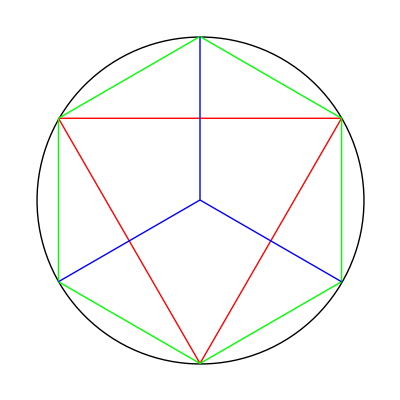

```mathematica
a = {0, -4};
c = a.RotationMatrix[2π/3];
b = a.RotationMatrix[-2π/3];
z = {0, 0};
a2 = a.RotationMatrix[π/3];
b2 = b.RotationMatrix[π/3];
c2 = c.RotationMatrix[π/3];
Graphics[{Circle[z, 4],Red,Line[{a, c}], Line[{a, b}], Line[{b, c}],Green, Line[{a, a2}], Line[{a2, c}],  Line[{c, c2}], Line[{c2, b}], Line[{b, b2}], Line[{b2, a}], Blue, Line[{z, a2}], Line[{z, b2}], Line[{z, c2}]}, PlotRange->5]
```

Bisecting each side of the triangle gives us six lines, which form a regular hexagon. This means that, given any regular polygon, we can double the number of sides of it by bisecting each side. So, say we wanted to draw a perfect 30-gon. To do this, you would draw the 15-gon as seen above, then bisect each of its sides using this method. Unfortunately, there is no way to trisect a side using Euclidean tools, so the most we can do is double the number of sides.

## What Regular Polygons can be Created?

We know that Euclid was able to construct perfect 3, 4, 5, 6, and 15-gons. Through the proof of the 15-gon, we know we can construct any mn-gon if m and n are relatively prime and we can construct a regular m-gon and n-gon. While checking if m and n are relatively prime is easy, how do we know which m and n-gons we can actually construct? Work on this question was performed by Gauss, and he was able to construct a 17-gon using the Euclidean tools.  So, we have 3, 5, and 17 in as values of m and n. It turns out that the only constructible n-gons with Euclidean Tools are when n is a Fermat prime, as proven in the Gauss-Wantzel theorem. Fermat primes are the numbers of the form 2^(2^k)+ 1. The only known Fermat primes are 3, 5, 17, 257, and 65537 (which is k = {0, 4} in the general form). So, the only n-gons that can be created are those such that:
n = {2^a * 3^b * 5^c * 17^d * 257^e * 65537^f | a ϵ Ν, {b, c, d, e, f} ϵ {0, 1}}
In other words, n can only have Fermat primes in its prime factorization no more than once, and it can have 2 as many times as it wants.
For instance, a 21-gon is not constructible since it can not be written in the above form (21’s prime factorization is 3^1 * 7^1 ).
But, a 160-gon is constructible (160 = 2^5 * 5^1). To do this, you would construct a regular pentagon, then perform the bisections above 5 times.
The smallest polygon that is not constructible is a 7-gon.
The largest regular polygon that can be constructed that has an odd number of sides is a 4,294,967,295-gon (which is 3*5*17*257*65537).